```mathematica
p=1/(4π d t)Exp[-r^2/(4 d t)]
```

(ⅇ^(-r^2/(4 d t)))/(4 d π t)

```mathematica
FullSimplify[D[p,t]-d 1/r D[r D[p,r],r]]
```

0

```mathematica
ptot=Assuming[{d>0,t>0},Integrate[2 π r p,{r,0,Infinity}]]
```

1

```mathematica
r p
```

(ⅇ^(-r^2/(4 d t)) r)/(4 d π t)

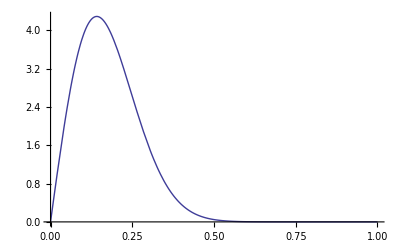

```mathematica
Plot[ 2π r p/.{d->0.001,t->10},{r,0,1}]
```

```mathematica
Assuming[γ>0,Integrate[1/γ Exp[-r^2/γ],{r,-Infinity,Infinity}]]
```

(√π)/(√γ)

```mathematica
Assuming[γ>0,Integrate[1/(√(π γ))Exp[-r^2/γ],{r,-Infinity,Infinity}]]
```

1